#### This script roughly reproduces the BL1g tauB curve; not perfect Parameters in Region 4 with gamma 1 - s0 ~ -0.07 - linear s(z)= s0 - z s0 / N - so that s(0) = s0, and s(N) = 0

```mathematica
ClearAll["Global`*"]
```

ⅇ^(Nval s0 (z/Nval-(0.5 z^2)/Nval^2))

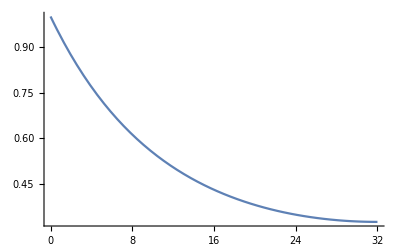

```mathematica
Psi = Exp[s0  Nval(z/Nval - 0.5*(z/Nval)^2)]
Plot[Psi/.{s0->-0.07, Nval->32},{z,0,32}]
```

#### Analytic integration of psi - why does this plot have negative values for z/N < 0.5? the function being integrated is positive - the end result matches the numeric integration

```mathematica
integralOfPsi=Integrate[ Psi ,z]
```

(1.25331 ⅇ^(0.5 Nval s0) √Nval Erf[(0.707107 √s0 (-1. Nval+1. z))/(√Nval)])/(√s0)

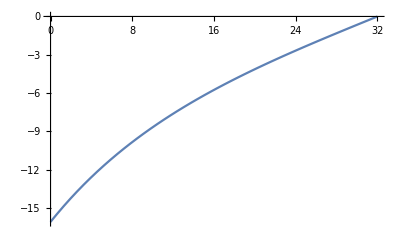

```mathematica
Plot[integralOfPsi/.{s0->-0.07, Nval->32},{z,0,32}]
```

```mathematica
probHitN=((integralOfPsi/.z->1) - (integralOfPsi/.z->0)) / ((integralOfPsi/.z->Nval)- (integralOfPsi/.z->0))
```

(-(1.25331 ⅇ^(0.5 Nval s0) √Nval Erf[(0.707107 (0.-1. Nval) √s0)/(√Nval)])/(√s0)+(1.25331 ⅇ^(0.5 Nval s0) √Nval Erf[(0.707107 (1.-1. Nval) √s0)/(√Nval)])/(√s0))/(0.-(1.25331 ⅇ^(0.5 Nval s0) √Nval Erf[(0.707107 (0.-1. Nval) √s0)/(√Nval)])/(√s0))

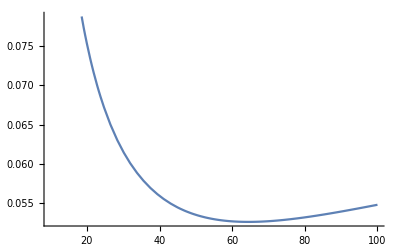

```mathematica
Plot[probHitN/.s0->-0.07,{Nval,10,100}]
```

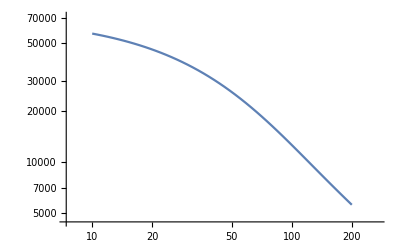

```mathematica
LogLogPlot[1/((10)^(-4) 0.145 Nval probHitN/.s0->-0.07),{Nval,10,200}]
```

#### Numeric integration of psi

```mathematica
integralOfPsiNum[Nv_, low_, high_]:=NIntegrate[Psi/.{s0->-0.07, Nval->Nv},{z,low,high}]
```

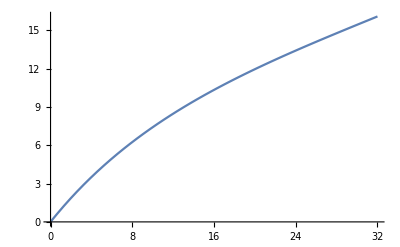

```mathematica
Plot[integralOfPsiNum[32,0,z],{z,0,32}]
```

```mathematica
probHitNnum[Nv_]:=integralOfPsiNum[Nv,0,1] / integralOfPsiNum[Nv,0,Nv]
```

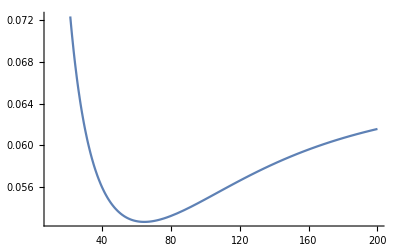

```mathematica
Plot[probHitNnum[Nval],{Nval,10,200}]
```

```mathematica
mfptNum=Table[1/((10)^(-4) 0.2 Nval probHitNnum[Nval]),{Nval,10,50}];
```

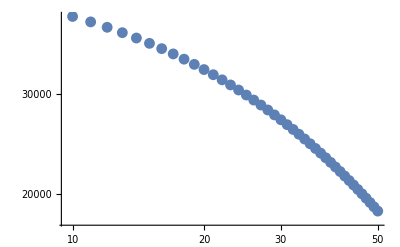

```mathematica
ListLogLogPlot[mfptNum, DataRange->{10,50}]
```

### Simplification of the tau_B integrals n the supp

```mathematica
params4 = {z1->0.4,s0->-0.06, s1->0.05}
params3 = {z1->0.4,s0->0.04, s1->-0.04}
```

{z1→0.4,s0→-0.06,s1→0.05}

{z1→0.4,s0→0.04,s1→-0.04}

```mathematica
A = -(s0 z + z^2 (s1-s0)/(2 z1));
B = -s1  (z-z1) / (1-z1) (1-(z+z1)/2);
```

```mathematica
term1 = Integrate[Exp[Nv A],{z,0,z1}]
factor2 = Exp[-Nv z1 (s1+s0)/2]
term2 = Integrate[Exp[Nv B],{z,z1,1}]
```

(ⅇ^(-(Nv s0^2 z1)/(2 (s0-s1))) √(π/2) √z1 (Erfi[(√Nv s0 √z1)/(√2 √(s0-s1))]-Erfi[(√Nv s1 √z1)/(√2 √(s0-s1))]))/(√Nv √(s0-s1))

ⅇ^(-1/2 Nv (s0+s1) z1)

-(ⅇ^(1/2 Nv s1 (-1+z1)) √(π/2) √(-1+z1) Erf[(√Nv √s1 √(-1+z1))/(√2)])/(√Nv √s1)

```mathematica
Plot[term2/.params4/.{N->Nval},{Nval,10,100}]
```

-Graphics-

```mathematica
intFull = term1 + factor2 term2
```

-(ⅇ^(1/2 Nv s1 (-1+z1)-1/2 Nv (s0+s1) z1) √(π/2) √(-1+z1) Erf[(√Nv √s1 √(-1+z1))/(√2)])/(√Nv √s1)+(ⅇ^(-(Nv s0^2 z1)/(2 (s0-s1))) √(π/2) √z1 (Erfi[(√Nv s0 √z1)/(√2 √(s0-s1))]-Erfi[(√Nv s1 √z1)/(√2 √(s0-s1))]))/(√Nv √(s0-s1))

```mathematica
(* region 3 simplification *)
R3 = FullSimplify[intFull, {s0>0, s1<0, 0<z1<1}]
```

(2 √(s1 z1) DawsonF[s0 √((Nv z1)/(2 s0-2 s1))]-2 ⅇ^(-1/2 Nv (s0+s1) z1) √(s1 z1) DawsonF[s1 √((Nv z1)/(2 s0-2 s1))]-ⅇ^(-1/2 Nv (s1+s0 z1)) √π √((s0-s1) (-1+z1)) Erf[(√Nv √s1 √(-1+z1))/(√2)])/(√2 √(Nv (s0-s1)) √s1)

```mathematica
(* region 4 simplification *)
R4 = FullSimplify[intFull, {s0<0, 1>s1>0, 0<z1<1}]
```

(√(π/2) (-ⅇ^(-1/2 Nv (s1+s0 z1)) √((-1+z1)/s1) Erf[(√(Nv s1) √(-1+z1))/(√2)]+(ⅇ^(-(Nv s0^2 z1)/(2 s0-2 s1)) z1 (Erfi[(s0 √(Nv z1))/(√2 √(s0-s1))]-Erfi[(s1 √(Nv z1))/(√2 √(s0-s1))]))/(√((s0-s1) z1))))/(√Nv)

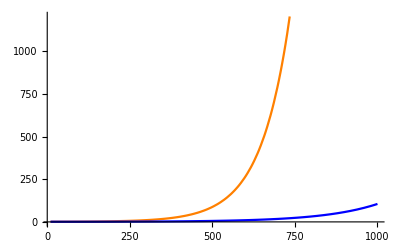

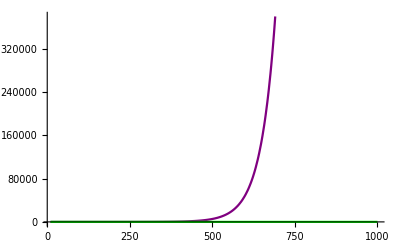

```mathematica
(* whole expression *)
Plot[{R3/.params3,R4/.params4 },{Nv,10,1000}, PlotStyle->{Orange, Blue}]
Plot[{R4guess1/.params4, R4guess2/.params4},{Nv,10,1000}, PlotStyle->{Purple, Green}]
```

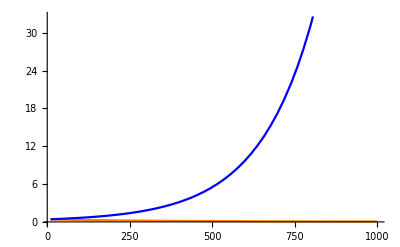

```mathematica
(* first term *)
Plot[{term1/.params3,term1/.params4},{Nv,10,1000}, PlotStyle->{Orange, Blue}]
```

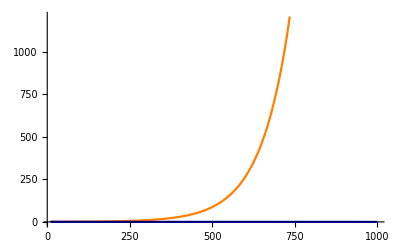

```mathematica
(* second term integral *)
Plot[{term2/.params3,term2/.params4},{Nv,10,1000}, PlotStyle->{Orange, Blue}]
```

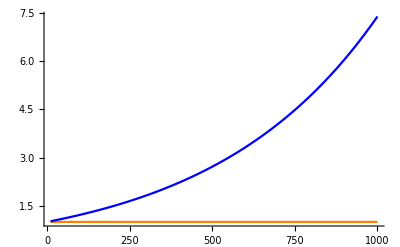

```mathematica
(* second term prefactor *)
Plot[{factor2/.params3,factor2/.params4},{Nv,10,1000}, PlotStyle->{Orange, Blue}]
```

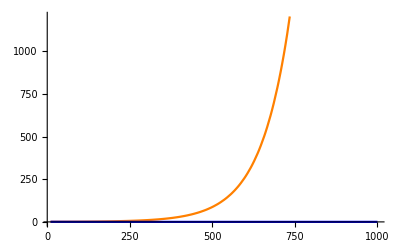

```mathematica
(* second term full (integral *prefactor) *)
Plot[{factor2*term2/.params3,factor2*term2/.params4},{Nv,10,1000}, PlotStyle->{Orange, Blue}]
```

#### taylor expand at large N

```mathematica
R4/.params4/.Nv->1/ϵ // Simplify
```

(ⅇ^(-0.013/ϵ) (2.38998 ⅇ^(0.0195455/ϵ) Erf[0.06742 √(1/ϵ)]+2.38998 ⅇ^(0.0195455/ϵ) Erf[0.080904 √(1/ϵ)]+4.34161 Erfi[0.122474 √(1/ϵ)]))/(√(1/ϵ))

```mathematica
Integrate[Exp[ x^2+ x],{x,0,1}]
```

(√π (-Erfi[1/2]+Erfi[3/2]))/(2 ⅇ^(1/4))

```mathematica
Manipulate[Plot[Exp[-Nv (a x^2+b x+c)],{x,0,1}],{Nv,10,1000},{a,-2,2},{b,-2,2},{c,-1,1}]
```

```mathematica
Manipulate[Plot[Exp[-Nv (a x^2+b x+c)],{x,0,1}],{Nv,10,1000},{a,-2,2},{b,-2,2},{c,-1,1}]
```

### Write as az^2+bz+c for each integral

```mathematica
Collect[A, z]
Collect[B, z]
```

-s0 z+((s0-s1) z^2)/(2 z1)

-(s1 z)/(1-z1)+(s1 z^2)/(2 (1-z1))-(s1 (-z1+z1^2/2))/(1-z1)

```mathematica
Collect[A/.params3, z]
Collect[B/.params3, z]
```

-0.04 z+0.1 z^2

-0.0213333+0.0666667 z-0.0333333 z^2

```mathematica
Collect[A/.params4, z]
Collect[B/.params4, z]
```

0.06 z-0.1375 z^2

0.0266667-0.0833333 z+0.0416667 z^2

```mathematica
Collect[B, z]
```

-(s1 z)/(1-z1)+(s1 z^2)/(2 (1-z1))-(s1 (-z1+z1^2/2))/(1-z1)

```mathematica
Solve[D[A,z]==0,z]/.params3
Solve[D[A,z]==0,z]/.params4
```

{{z→0.2}}

{{z→0.218182}}

```mathematica
Solve[D[B,z]==0,z]/.params3
Solve[D[B,z]==0,z]/.params4
```

{{z→1}}

{{z→1}}

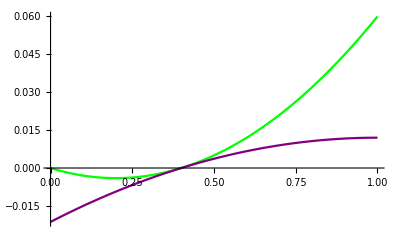

```mathematica
Plot[{A/.params3, B/.params3}, {z,0,1}, PlotStyle->{Green, Purple}]
```

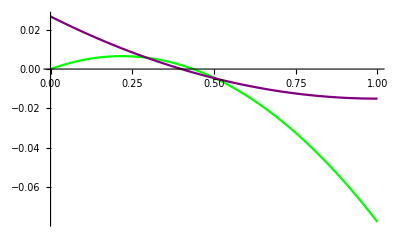

```mathematica
Plot[{A/.params4, B/.params4}, {z,0,1}, PlotStyle->{Green, Purple}]
```

```mathematica
B
```

-(s1 (1+1/2 (-z-z1)) (z-z1))/(1-z1)

```mathematica
Plot[{A/.{z1->0.4, s0->-0.06, s1->0.05}, B+z1 (s1+s0)/2/.{z1->0.4, s0->-0.05, s1->0.05}}, {z,0,1}, PlotStyle->{Green, Purple}]
```

-Graphics-

```mathematica
Solve[0==A, z]
```

{{z→0},{z→(2 s0 z1)/(s0-s1)}}

```mathematica
Collect[B+z1 (s1+s0)/2 ,z]
```

-(s1 z)/(1-z1)+(s1 z^2)/(2 (1-z1))+1/2 (s0+s1) z1+(s1 z1)/(1-z1)-(s1 z1^2)/(2 (1-z1))

```mathematica
N[term1/.{z1->0.4,s0->-0.6, s1->0.05}/.N->102]
```

-((0.+0.98318 ⅈ) 2.71828^(0.110769 Nv) ((0.+1. ⅈ) Erf[(0.027735+0. ⅈ) √Nv]+(0.+1. ⅈ) Erf[(0.33282+0. ⅈ) √Nv]))/(√Nv)

```mathematica
FullSimplify[term1,{s1>0,s0<0}]
```

(ⅇ^(-(Nv s0^2 z1)/(2 (s0-s1))) √(π/2) √z1 (Erfi[(√Nv s0 √z1)/(√2 √(s0-s1))]-Erfi[(√Nv s1 √z1)/(√2 √(s0-s1))]))/(√Nv √(s0-s1))

#### saddle point for term 1, region 4

```mathematica
maximizer = Solve[D[A,z]==0,z][[1]]
```

{z→(s0 z1)/(s0-s1)}

```mathematica
saddlepointTerm1 = Exp[-Nv A/.maximizer]
```

ⅇ^(-Nv (-(s0^2 z1)/(s0-s1)-(s0^2 (-s0+s1) z1)/(2 (s0-s1)^2)))

### Simplify full expression for Region 4

```mathematica
R4 // Expand
R4 /.params4 // Simplify // Expand
```

-(ⅇ^(-1/2 Nv (s1+s0 z1)) √(π/2) √((-1+z1)/s1) Erf[(√(Nv s1) √(-1+z1))/(√2)])/(√Nv)+(ⅇ^(-(Nv s0^2 z1)/(2 s0-2 s1)) √(π/2) √((s0-s1) z1) Erfi[(s0 √(Nv z1))/(√2 √(s0-s1))])/(√Nv (s0-s1))-(ⅇ^(-(Nv s0^2 z1)/(2 s0-2 s1)) √(π/2) √((s0-s1) z1) Erfi[(s1 √(Nv z1))/(√2 √(s0-s1))])/(√Nv (s0-s1))

(2.38998 ⅇ^(0.00654545 Nv) Erf[0.06742 √Nv])/(√Nv)+(2.38998 ⅇ^(0.00654545 Nv) Erf[0.080904 √Nv])/(√Nv)+(4.34161 ⅇ^(-0.013 Nv) Erfi[0.122474 √Nv])/(√Nv)

```mathematica
R4guess1= Integrate[Exp[-Nv (s0 z)], {z,0,z1}]
R4guess2 =2 Sqrt[(π (1.3)/Nv)]Exp[Nv ((1.3)^2 0.06^2)]
```

(1-ⅇ^(-Nv s0 z1))/(Nv s0)

4.04182 ⅇ^(0.006084 Nv) √(1/Nv)

```mathematica
(* check which terms in the evaluation of I1 are larger *)
Manipulate[Plot[{-s0 / Sqrt[s1-s0], Sqrt[s1-s0],Sqrt[z1/(2(s1-s0))]} , {z,0,1}, 
PlotStyle->{Green, Purple, Orange}],
{s0,-1,0.0001},{s1,0.0001,1}, {z1,0.0001,1}]
```

-Graphics-

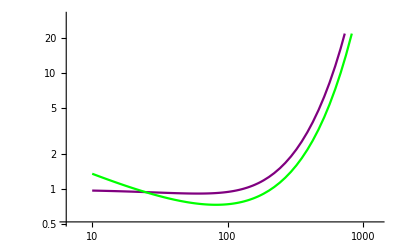

```mathematica
(* whole expression *)
Plot[{R3/.params3,R4/.params4 },{Nv,10,1000}, PlotStyle->{Orange, Blue}]
LogLogPlot[{R4/.params4, R4guess2},{Nv,10,1000}, PlotStyle->{Purple, Green}]
```

```mathematica
R4guess2
```

(√(π/2) √z1 Erfi[(√Nv √(s0-s1) √z1)/(√2)])/(√Nv √(s0-s1))

### Simplify full expression for Region 3

```mathematica
R3 // Expand
R3 /.params4 // Simplify // Expand
```

(√2 √(Nv (s0-s1)) √(s1 z1) DawsonF[s0 √((Nv z1)/(2 s0-2 s1))])/(Nv (s0-s1) √s1)-(√2 ⅇ^(-1/2 Nv (s0+s1) z1) √(Nv (s0-s1)) √(s1 z1) DawsonF[s1 √((Nv z1)/(2 s0-2 s1))])/(Nv (s0-s1) √s1)-(ⅇ^(-1/2 Nv (s1+s0 z1)) √(π/2) √(Nv (s0-s1)) √((s0-s1) (-1+z1)) Erf[(√Nv √s1 √(-1+z1))/(√2)])/(Nv (s0-s1) √s1)

(2.6968 ⅇ^(0.002 Nv) √-Nv DawsonF[0.06742 √-Nv])/Nv+(2.6968 √-Nv DawsonF[0.080904 √-Nv])/Nv+((0.+4.34161 ⅈ) ⅇ^(-0.013 Nv) √-Nv Erfi[0.122474 √Nv])/Nv

```mathematica
R3guess1= Integrate[Exp[-Nv (s0 z)], {z,0,z1}]
R3guess2 =2 Sqrt[(π (1.3)/Nv)]Exp[Nv ((1.3)^2 0.06^2)]
```

(1-ⅇ^(-Nv s0 z1))/(Nv s0)

4.04182 ⅇ^(0.006084 Nv) √(1/Nv)

```mathematica
(* check which terms in the evaluation of I1 are larger *)
Manipulate[Plot[{-s0 / Sqrt[s1-s0], Sqrt[s1-s0],Sqrt[z1/(2(s1-s0))]} , {z,0,1}, 
PlotStyle->{Green, Purple, Orange}],
{s0,-1,0.0001},{s1,0.0001,1}, {z1,0.0001,1}]
```

```mathematica
(* whole expression *)
Plot[{R3/.params3,R4/.params4 },{Nv,10,1000}, PlotStyle->{Orange, Blue}]
LogLogPlot[{R3/.params4, R3guess2},{Nv,10,1000}, PlotStyle->{Purple, Green}]
```

-Graphics-

-Graphics-

```mathematica
R3guessNoFeedback= √(π/(2 Nv s0))Exp[-Nv s0/2] Erfi[√(Nv (s0)/2)  ]
R3guessFeedback1= √(1/(2 Nv D))Exp[Nv D(z1-(s1^2+1)/2)]Erfi[√(Nv (-s1)/2 (1-z1)) ] /.D->(-s1)/(1-z1)
R3guessFeedback2= 1/Nv * √(1/(2 s1^2))Exp[Nv (1-z1) (-s1)]
```

ⅇ^(-(Nv s0)/2) √(π/2) √(1/(Nv s0)) Erfi[(√(Nv s0))/(√2)]

(ⅇ^(-(Nv s1 (1/2 (-1-s1^2)+z1))/(1-z1)) √(-(1-z1)/(Nv s1)) Erfi[(√(-Nv s1 (1-z1)))/(√2)])/(√2)

(ⅇ^(-Nv s1 (1-z1)) √(1/s1^2))/(√2 Nv)

```mathematica
Manipulate[LogLogPlot[R3guess1 /.{z1->z1V, s1->s1V}, {Nv,10,1000}, 
PlotStyle->{Green}],
{s1V,-1,-0.0001}, {z1V,0.0001,1}]
```

```mathematica
Manipulate[LogLogPlot[{R3guessFeedback1 /.{z1->z1V, s1->s1V,s0->s0V}, R3guessFeedback2/.{z1->z1V, s1->s1V}}, {Nv,10,1000}, 
PlotStyle->{Green, Blue}],
{s0V,0.0001, 1}, {s1V,-1,-0.0001}, {z1V,0.0001,1}]
```

```mathematica
LogLogPlot[R3guessNoFeedback2->{z1->0.4, s1->-0.04}, {Nv,10,1000}, 
PlotStyle->{Green, Blue}]
```

-Graphics-

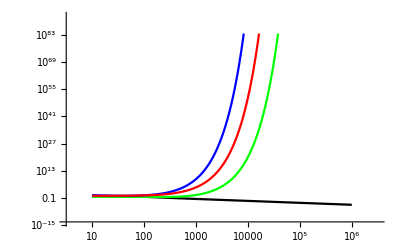

```mathematica
LogLogPlot[{R3guessNoFeedback/.params3, R3guessFeedback1 /.params3, R3guessFeedback2/.params3, R3/.params3}, {Nv,10,1000000}, 
PlotStyle->{Black, Green, Blue, Red}]
```

```mathematica
R3
```

(2 √(s1 z1) DawsonF[s0 √((Nv z1)/(2 s0-2 s1))]-2 ⅇ^(-1/2 Nv (s0+s1) z1) √(s1 z1) DawsonF[s1 √((Nv z1)/(2 s0-2 s1))]-ⅇ^(-1/2 Nv (s1+s0 z1)) √π √((s0-s1) (-1+z1)) Erf[(√Nv √s1 √(-1+z1))/(√2)])/(√2 √(Nv (s0-s1)) √s1)

```mathematica
R3guessNoFeedback
```

ⅇ^(-(Nv s0)/2) √(π/2) √(1/(Nv s0)) Erfi[(√(Nv s0))/(√2)]